Discrete Distribution

A single random number taken drawn from the Bernoulli distribution with probability of success equal to 0.3:

```mathematica
RandomVariate[BernoulliDistribution[0.3],1]
```

{1}

Now we sample 4 numbers according to the Bernoulli distribution:

```mathematica
rndseq=RandomVariate[BernoulliDistribution[0.3],4]
```

{0,1,0,0}

Notice that “1” means success, and “0” not success.

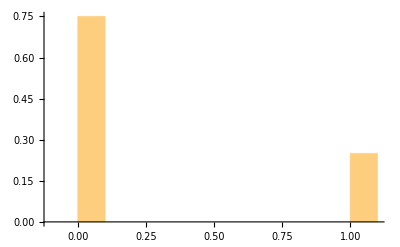

```mathematica
Histogram[rndseq,{-0.1,1.1,0.1},"Probability"]
```

```mathematica
N[Mean[rndseq]]
```

0.25

We now generate 200 samples, each having 4 samples of random numbers drawn from a Bernoulli distribution with parameter p, and we calculate the arithmetic mean for each of the samples:

```mathematica
p=0.3;(*probability of success*)
nsample1=4;(*size of the sample*)
nrepeat=1000;(*we repeat the experiment 1000 times*)
meansamp[p_,nsample_]:=N[Mean[RandomVariate[BernoulliDistribution[p],nsample]]]
reslist=Table[meansamp[p,nsample1],  nrepeat];
```

The result is a list of 200 elements, each containing the mean of each of the 1000 samples. We can inspect e.g. the 10 first elements:

```mathematica
reslist[[1;;10]]
```

{0.,0.5,0.25,0.,0.,0.5,0.25,0.25,0.25,0.5}

Now we look at how they means of the samples are distributed:

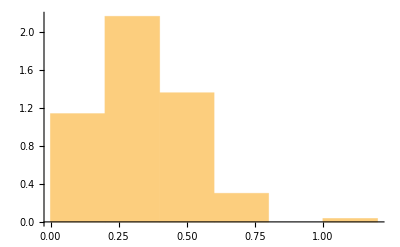

```mathematica
Histogram[reslist,Automatic,"PDF"]
```

The Bernoulli distribution with p=0.3 has the following expected value, variance and standard deviation:

```mathematica
mu=Expectation[x,x\[Distributed]BernoulliDistribution[p]]
```

0.3

```mathematica
var=Variance[BernoulliDistribution[p]]
```

0.21

```mathematica
std=Sqrt[var]
```

0.458258

We now compare the empirically obtained distribution with the normal distribution we expect from the CLT:

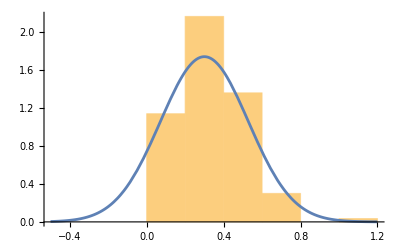

```mathematica
plot1=Show[{
Histogram[reslist,Automatic,"PDF",PlotRange->{{-0.5,1.2},All}],
Plot[PDF[NormalDistribution[mu,std/Sqrt[nsample1]],x],{x,-0.5,1.2}]
}]
```

Now we increase the size of each of the samples to 50:

```mathematica
p=0.3;(*probability of success*)
nsample2=50;(*size of the sample*)
nrepeat=1000;(*we repeat the experiment 1000 times*)
meansamp[p_,nsample_]:=N[Mean[RandomVariate[BernoulliDistribution[p],nsample]]]
reslist50=Table[meansamp[p,nsample2],  nrepeat];
```

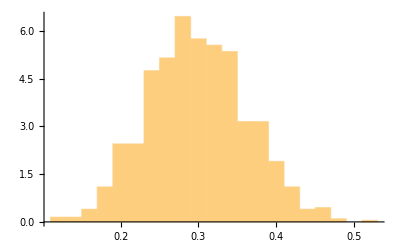

```mathematica
Histogram[reslist50,Automatic,"PDF"]
```

We now compare the empirically obtained distribution with the normal distribution with expect from the CLT. Notice that because we have increase the sample size of each of the samples, we expect the standard deviation to decrease and the distribution of the sample mean to be better approximated by the  normal distribution:

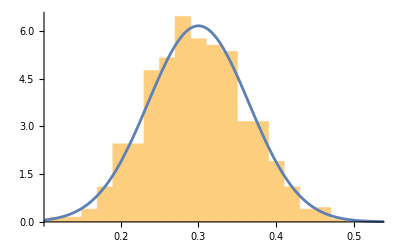

```mathematica
plot2=Show[{Histogram[reslist50,Automatic,"PDF"],Plot[PDF[NormalDistribution[mu,std/Sqrt[nsample2]],x],{x,-0.1,1.}]
}]
```

Now we plot the two obtained histograms using the same scale for comparison:

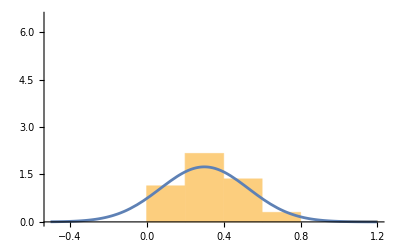

```mathematica
plot1b=plot1=Show[{
Histogram[reslist,Automatic,"PDF",PlotRange->{{-0.5,1.2},{0,6.5}}],
Plot[PDF[NormalDistribution[mu,std/Sqrt[nsample1]],x],{x,-0.5,1.2}]
}]
```

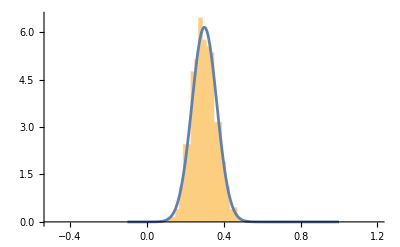

```mathematica
plot2b=Show[{Histogram[reslist50,Automatic,"PDF",PlotRange->{{-0.5,1.2},{0,6.5}}],Plot[PDF[NormalDistribution[mu,std/Sqrt[nsample2]],x],{x,-0.1,1.}]
}]
```

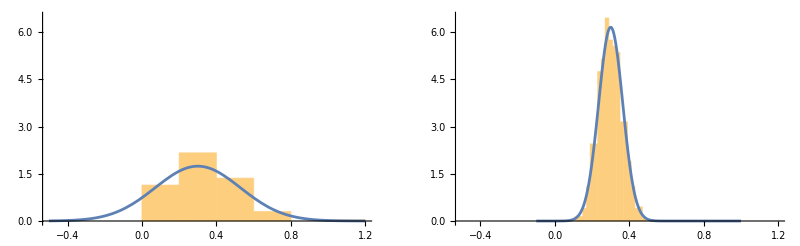

```mathematica
GraphicsRow[{plot1b,plot2b}]
```

Continuous Distribution

We now assume that we draw numbers from a triangular distribution. How does the distribution of the sample mean look like when we increase the sample size?

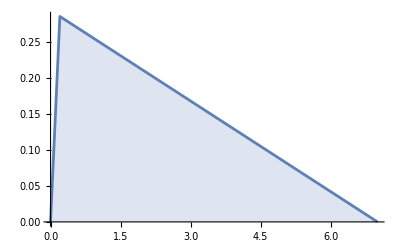

```mathematica
Plot[PDF[TriangularDistribution[{0,7},0.2],x] ,{x,0,7},Filling->Axis,Exclusions->None]
```

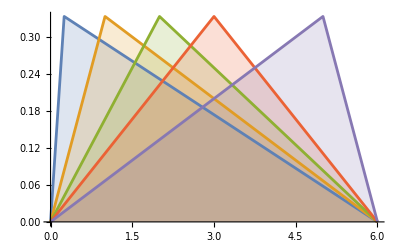

```mathematica
Plot[Table[PDF[TriangularDistribution[{0,6},c],x],{c,{1/4,1,2,3,5}}]//Evaluate,{x,0,6},Filling->Axis,Exclusions->None]
```

Let’s work for our example with range [0,6] and maximum at 0.25:

```mathematica
tridis=TriangularDistribution[{0,6},1/4];
```

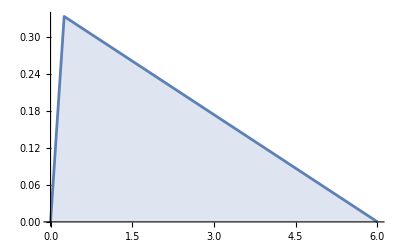

```mathematica
Plot[PDF[tridis,x] ,{x,0,6},Filling->Axis,Exclusions->None]
```

We now take 10,000 samples of size n and calculate the mean for each of them. We want to explore how the distribution of the sample mean is distributed as we change the sample size n:

```mathematica
meansample[n_]:=Mean[RandomVariate[tridis,n]]
nrepeat=10000;
```

```mathematica
n=1;
reslist1=Table[meansample[n],  nrepeat];
```

```mathematica
n=2;
reslist2=Table[meansample[n],  nrepeat];
```

```mathematica
n=3;
reslist3=Table[meansample[n],  nrepeat];
```

```mathematica
n=4;
reslist4=Table[meansample[n],  nrepeat];
```

```mathematica
n=5;
reslist5=Table[meansample[n],  nrepeat];
```

```mathematica
n=10;
reslist10=Table[meansample[n],  nrepeat];
```

```mathematica
n=100;
reslist100=Table[Mean[RandomVariate[tridis,ntrials]],  nrepeat];
```

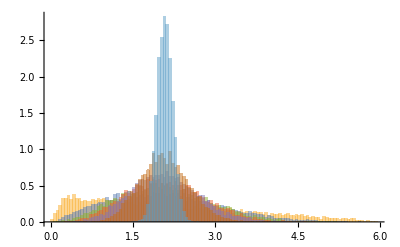

```mathematica
Histogram[{reslist1,reslist2,reslist3,reslist4,reslist5,reslist10,reslist100},100,"PDF"]
```

Now we can compare the obtained histograms with the normal distributions we would expect for the different sample sizes:

```mathematica
mu=N[Expectation[x,x\[Distributed]tridis]]
```

2.08333

```mathematica
std=N[StandardDeviation[tridis]]
```

1.38569

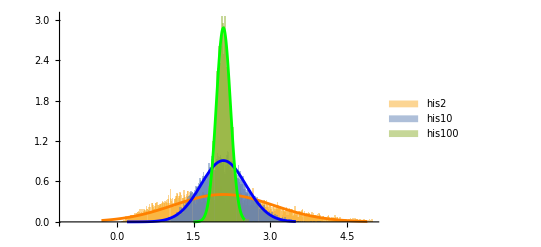

```mathematica
Show[{
Histogram[{reslist2,reslist10,reslist100},{-1,5,0.01},"PDF",ChartLegends->{"his2","his10","his100"}],
Plot[PDF[NormalDistribution[mu,std/Sqrt[2]],x],{x,-0.3,4.9},PlotStyle->Orange],
Plot[PDF[NormalDistribution[mu,std/Sqrt[10]],x],{x,0.2,3.5},PlotStyle->Blue],
Plot[PDF[NormalDistribution[mu,std/Sqrt[100]],x],{x,1.5,2.5},PlotStyle->Green]
}]
```